```mathematica
myFactor[n_]:=Join[Flatten[Table[Table[f[[1]],{i,1,1 f[[2]]}],{f,FactorInteger[n]}]],1]
```

```mathematica
myDistinctFactor[12]
```

{2,3}

```mathematica
myDistinctFactor[n_]:=DeleteDuplicates[myFactor[n]]
```

```mathematica
magicGraham[primes]
```

1+∑_p^primes Log[(1+p)/(2 p)]/Log[p]

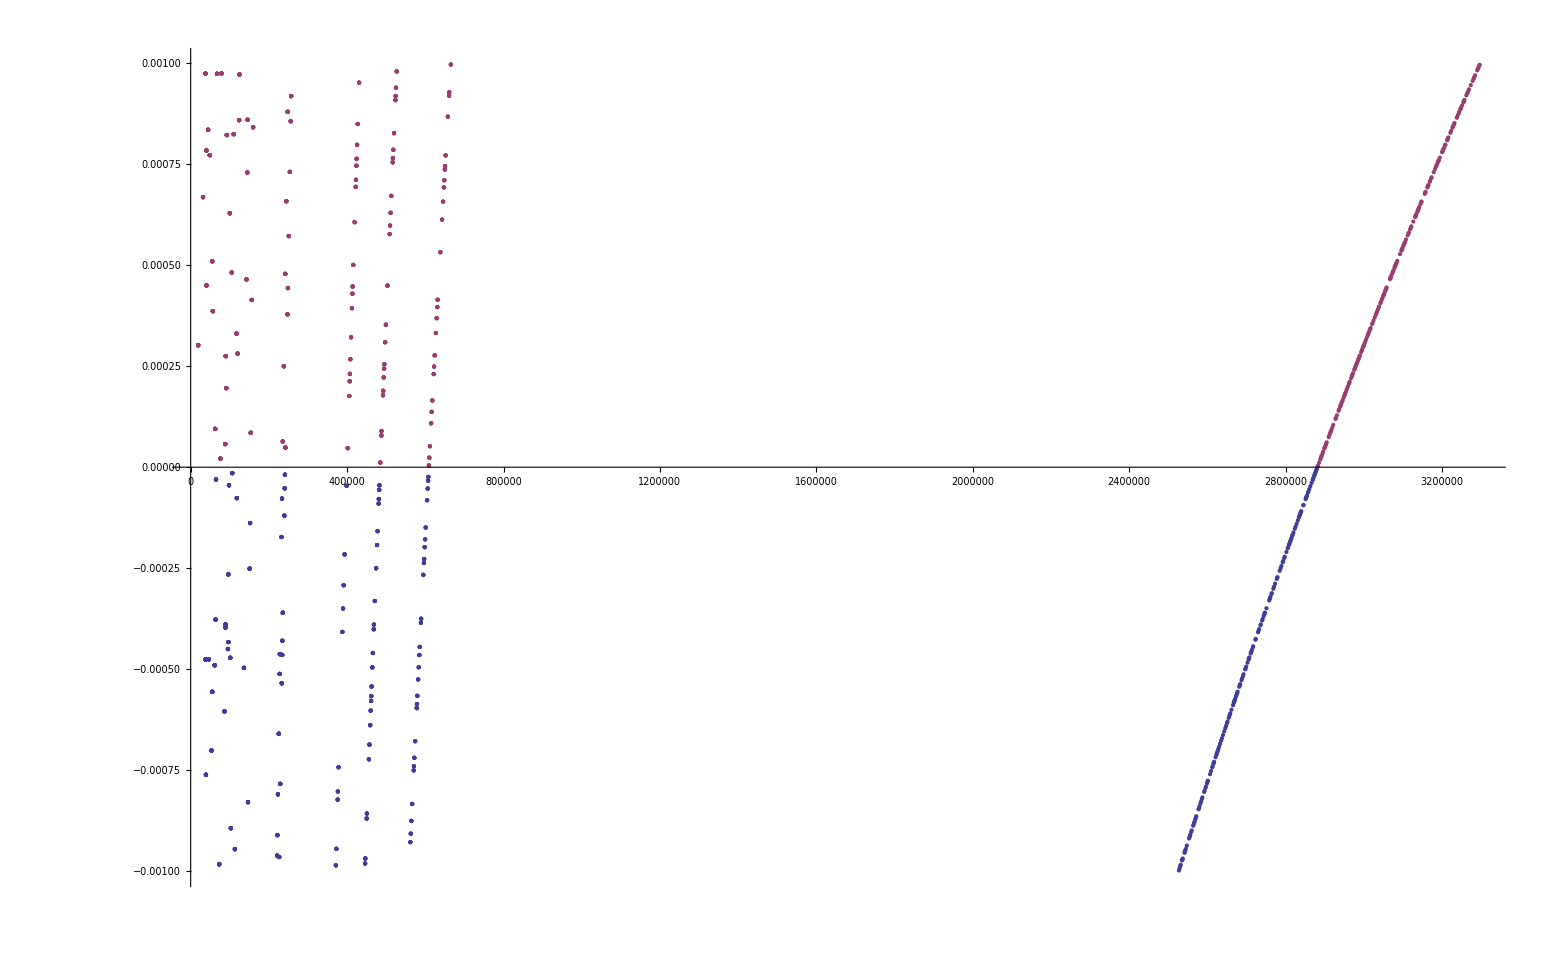

```mathematica
ListPlot[
With
[{primes = Monitor[
Select[Table[myDistinctFactor[i],{i,1,7000000}],Length[#]==4 && #[[1]]≠2&]
,i]},
With[
{all=Select[Table[{Product[p,{p,current}],N[magicGraham[current]]},{current,primes}],Abs[#[[2]]]<0.00001&]},
{
Map[Tooltip[#,myDistinctFactor[#[[1]]]]&,Select[all,#[[2]]<0 && Abs[#[[2]]]<0.001&]],
Map[Tooltip[#,myDistinctFactor[#[[1]]]]&,Select[all,#[[2]]>0&& Abs[#[[2]]]<0.001&]]
}
]
] 
,Joined->False, PlotRange->All]
```

```mathematica
With
[{primes = Monitor[
Select[Table[myDistinctFactor[i],{i,1,7000000}],Length[#]==4 && #[[1]]≠2&]
,i]},
With[
{all=Select[Table[{Product[p,{p,current}],N[magicGraham[current]]},{current,primes}],Abs[#[[2]]]<0.00001&]},
Sort[all,#1[[2]]<#2[[2]]&]
]
]
```

{{2878005,-8.35821×10^-6},{2879565,-4.28666×10^-6},{2880345,-2.25189×10^-6},{2881905,1.81566×10^-6},{2882685,3.84844×10^-6},{609195,4.46136×10^-6},{609195,4.46136×10^-6},{609195,4.46136×10^-6},{609195,4.46136×10^-6}}

```mathematica
Module[
{bestGr=1000, best, current, factors, gr},
Monitor[
For[current=2, current < 10000000, current++,
factors = Sort[myDistinctFactor[current]];
If[factors[[1]]==2, Continue[]];
gr = N[magicGraham[factors]];
If[Abs[gr]<bestGr,
bestGr = Abs[gr];
best=factors;
Print[{best, gr}]
]
],
current
];
best
]
```

{{3},0.63093}

{{3,5},0.313536}

{{3,5,7},0.0259503}

{{5,11,13,23},-0.0190089}

{{7,11,13,17},-0.00618561}

{{7,11,13,19},0.000302007}

{{3,7,29,103},0.0000947964}

{{3,11,13,151},-0.0000304943}

{{3,7,23,157},0.0000212941}

{{3,5,41,173},-0.0000146799}

{{3,7,11,2099},0.0000113749}

{{3,5,17,2389},4.46136×10^-6}

{{3,5,13,14767},-4.28666×10^-6}

{{3,5,13,14771},-2.25189×10^-6}

{{3,5,13,14779},1.81566×10^-6}

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
Module[
{bestGr=1000, best, current, factors, gr},
Monitor[
For[current=10000000, current < 1000000000, current++,
factors = Sort[myDistinctFactor[current]];
If[factors[[1]]==2, Continue[]];
gr = N[magicGraham[factors]];
If[Abs[gr]<bestGr,
bestGr = Abs[gr];
best=factors;
Print[{best, gr}]
]
],
current
];
best
]
```

{{11,909091},0.696702}

{{3,5,666667},0.261847}

{{3,7,31,15361},0.0788409}

{{3,5,61,3643},0.0643875}

{{3,5,7,95239},-0.0345109}

{{3,5,11,60607},-0.00218458}

{{3,5,11,60611},-0.00218421}

{{3,5,11,60617},-0.00218364}

{{3,5,11,60623},-0.00218308}

{{3,5,13,17099},0.00108082}

{{3,7,11,2063},-0.000192803}

{{3,7,11,2069},-0.000158463}

{{3,5,19,1409},0.0000471529}

{{3,7,11,2089},-0.0000448972}

{{3,7,11,2099},0.0000113749}

{{3,5,17,2389},4.46136×10^-6}

{{3,5,13,14767},-4.28666×10^-6}

{{3,5,13,14771},-2.25189×10^-6}

{{3,5,13,14779},1.81566×10^-6}

{{3,5,11,90031},-1.57073×10^-6}

{{3,5,11,90053},-2.69673×10^-7}

{{3,5,11,90059},8.50948×10^-8}

$Aborted